# Function

## Temp

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]]//FullSimplify;
ans=Solve[den/CoefficientList[den,v][[3]]==0,v]//FullSimplify;
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)

]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])//Simplify
]
```

## 2Level

```mathematica
Lev2DoppTest[T_,P_,diam_] :=
Module[{d,Δ,Nat,γ21,Γ12,d21,ℏ,e0,c,wcn,wc,u,omegac,f,A,α1,α2,Zα,β1,β2,Zβ,f2,A2,omegac2,d21u,wupper},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
γ21=2*Pi*5.750056 10^6/2;
Γ12=2*Pi*5.750056 10^6;
d21=Sqrt[5/27]*2.537717 10^-29;
d21u=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac=(1/ℏ Sqrt[1/(e0 c)]*d21*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d21u*Sqrt[P/(Pi*(diam/2)^2)]); 
wupper=2Pi(-0.361*10^9);
Zα=c/wc (ⅈ γ21+Δ-wupper);
Zβ=c/wc (ⅈ γ21+Δ-wupper);
α1=(-(√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
α2=((√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
β1=(-(√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
β2=((√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
A= (c d21^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12);
A2= (c d21u^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12); 
f=A 1/(α1-α2)(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[√(1/u^2) α1]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[√(1/u^2) α2]-Log[-1/α2]-Log[α2]));
f2=A2 1/(β1-β2)(-ⅇ^(-β1^2/u^2) (Zβ+β1) (π Erfi[√(1/u^2) β1]-Log[-1/β1]-Log[β1])+ⅇ^(-β2^2/u^2) (Zβ+β2) (π Erfi[√(1/u^2) β2]-Log[-1/β2]-Log[β2]));
Transpose[{ d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[f+f2]]
}]

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=Lev4DoppTestsc[T,P,diam,gam,delt,ab]=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

# P=50

```mathematica
p=50;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

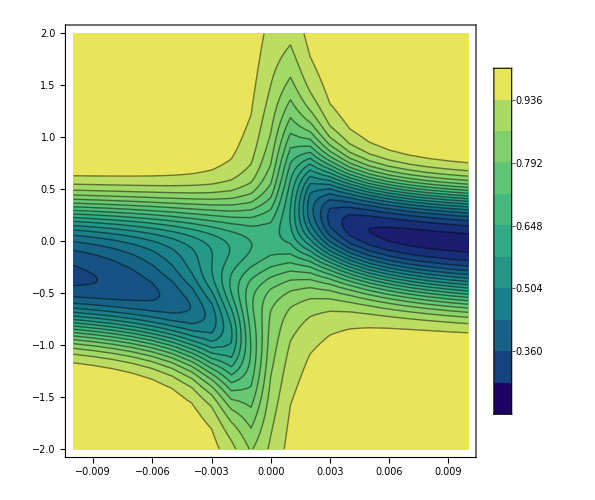
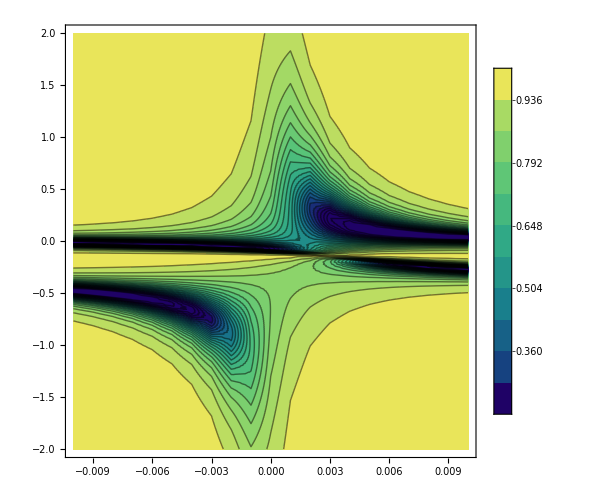
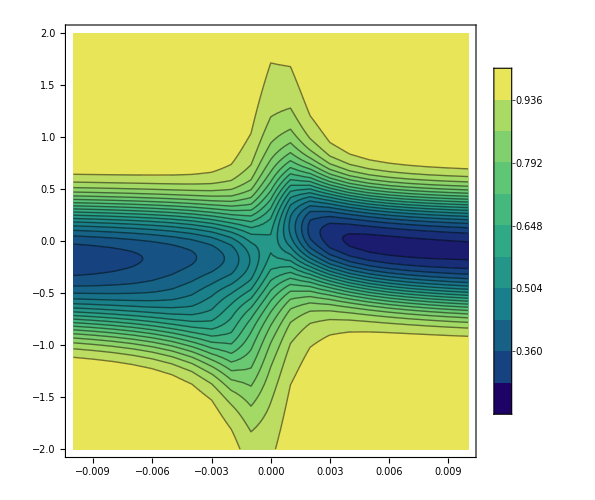
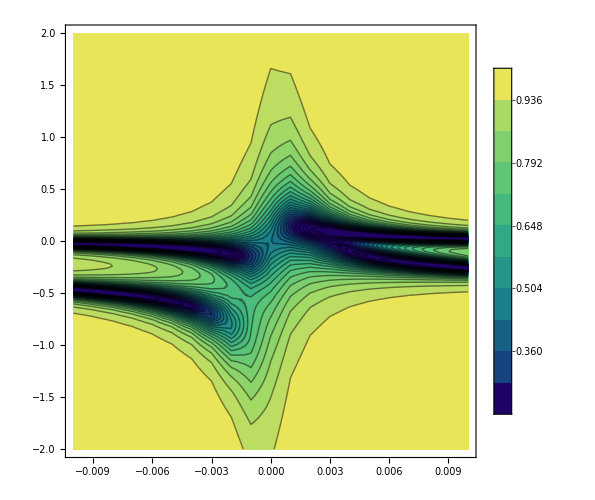
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

# P=10

```mathematica
p=10;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

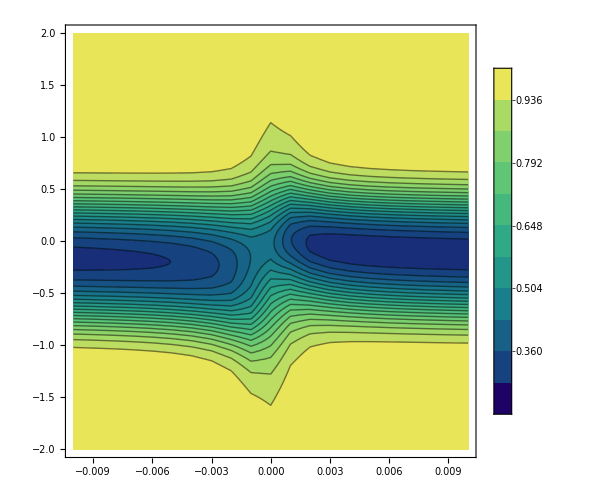
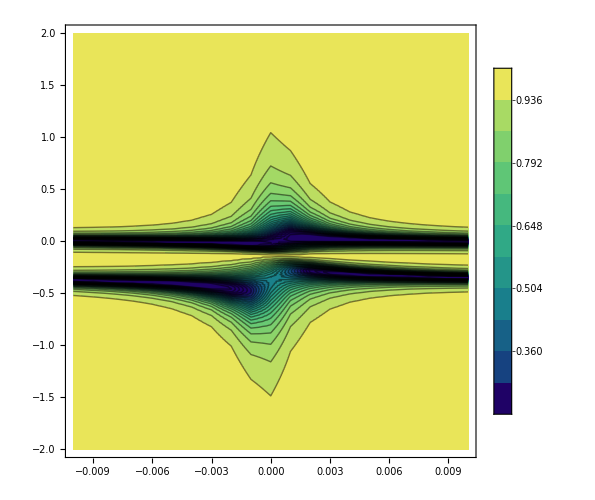
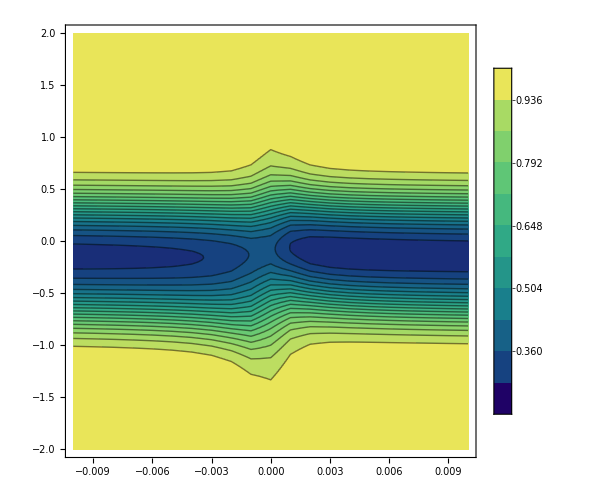
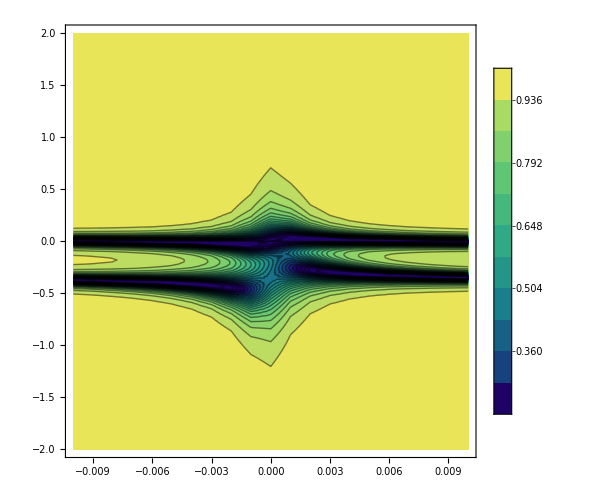
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

# P=1

```mathematica
p=1;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

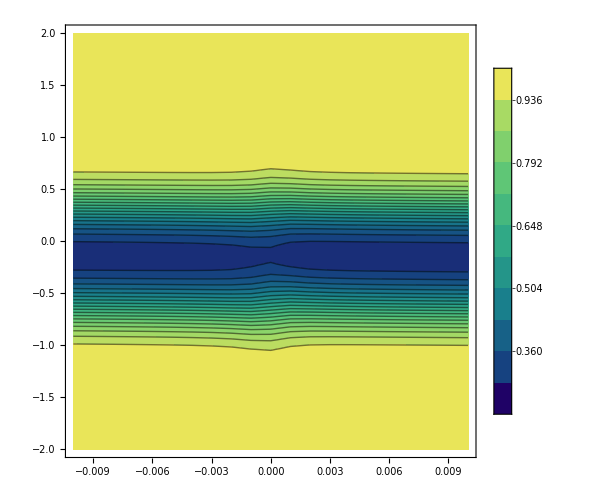
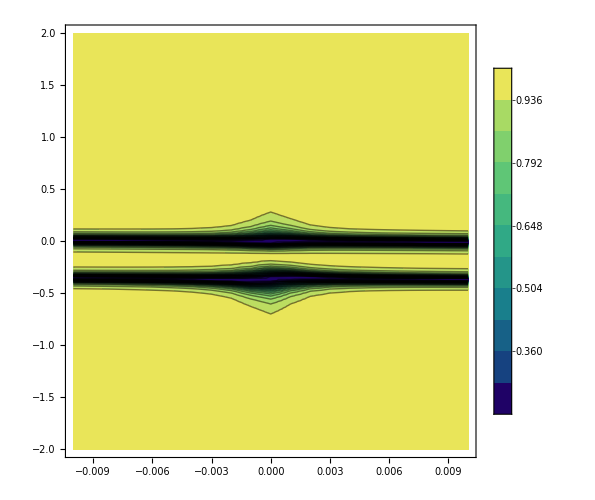
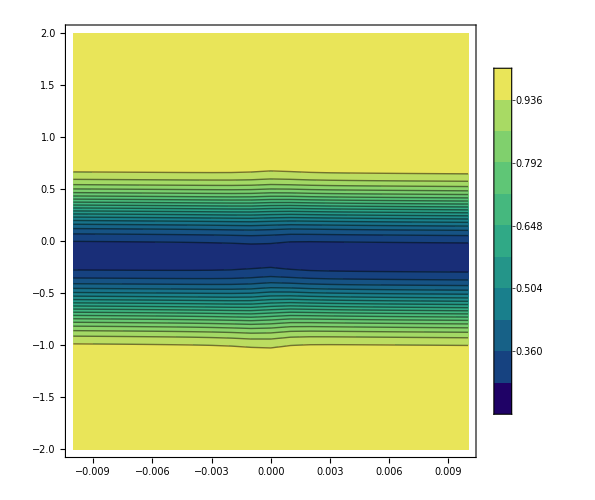
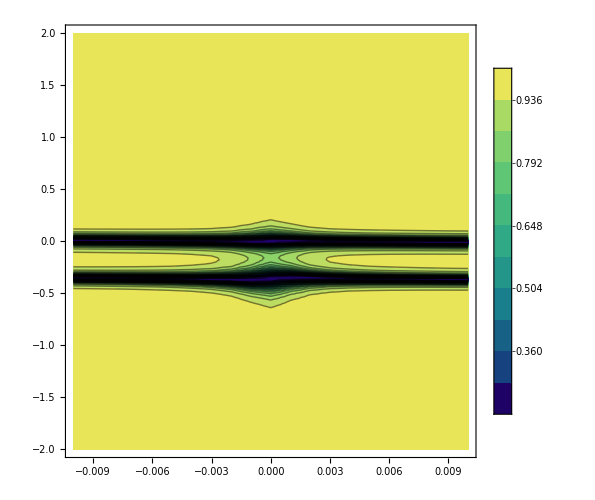
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

# P=0

```mathematica
p=0;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

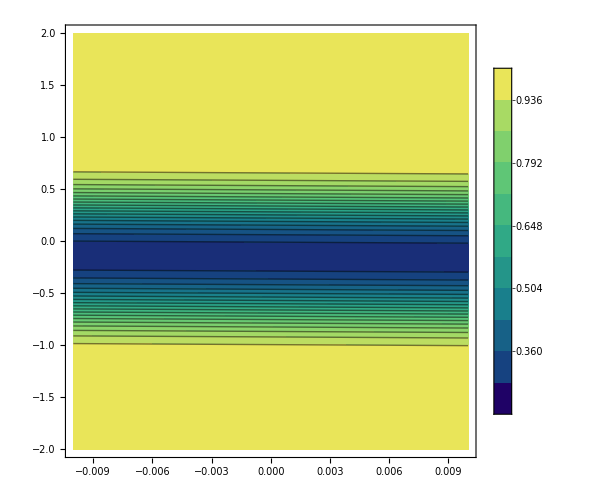
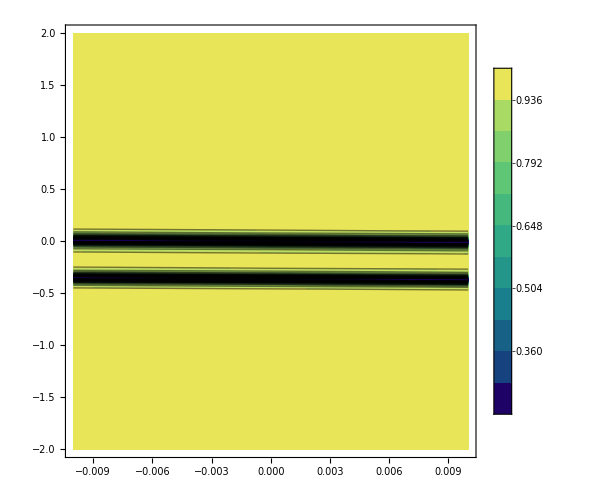
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

# Cross section

## P=10

```mathematica
p=10;
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.005],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.005]}]}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.005],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.005]}]}]],3];
res5=Interpolation[kkk5];
Kia5=ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
res7=Interpolation[kkk7];
Kia7=ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.005],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.005]}]}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.005],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.005]}]}]],3];
res6=Interpolation[kkk6];
Kia6=ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
res8=Interpolation[kkk8];
Kia8=ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kia6,
ParametricPlot[{t,b},{t,-0.2,0.2}],ImageSize->300],
Show[Kia8,
ParametricPlot[{t,b},{t,-0.2,0.2}],ImageSize->300]
,Plot[{res6[t,b],res8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kia6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kia8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{res6[b,t],res8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.02,0.02}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kia5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kia7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{res5[t,b],res7[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kia5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kia7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{res5[b,t],res7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.2,0.2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kia7,,ImageSize→300].

```mathematica
p=10;
kk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
re5=Interpolation[kk5];
Ki5=ListContourPlot[kk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
re7=Interpolation[kk7];
Ki7=ListContourPlot[kk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
kk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
re6=Interpolation[kk6];
Ki6=ListContourPlot[kk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
re8=Interpolation[kk8];
Ki8=ListContourPlot[kk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Ki6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Ki8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{re6[t,b],re8[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Ki6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Ki8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{re6[b,t],re8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Ki5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Ki7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{re5[t,b],re7[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Ki5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Ki7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{re5[b,t],re7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Ki7,,ImageSize→300].

## P=50

```mathematica
p=50;
kkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
kkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
resk5=Interpolation[kkkk5];
Kiak5=ListContourPlot[kkkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
resk7=Interpolation[kkkk7];
Kiak7=ListContourPlot[kkkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
kkkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
kkkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
resk6=Interpolation[kkkk6];
Kiak6=ListContourPlot[kkkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
resk8=Interpolation[kkkk8];
Kiak8=ListContourPlot[kkkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk6[t,b],resk8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk6[t,b],resk8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kiak7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{resk5[b,t],resk7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.2,0.2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk5[t,b],resk7[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

```mathematica
p=50;
kkl5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkl7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
rel5=Interpolation[kkl5];
Kil5=ListContourPlot[kkl5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
rel7=Interpolation[kkl7];
Kil7=ListContourPlot[kkl7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
kkl6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkl8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
rel6=Interpolation[kkl6];
Kil6=ListContourPlot[kkl6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
rel8=Interpolation[kkl8];
Kil8=ListContourPlot[kkl8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kil6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kil8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{rel6[b,t],rel8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kil8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{rel6[t,b],rel8[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kil7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{rel5[t,b],rel7[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kil7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{rel5[b,t],rel7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

## P=100

```mathematica
{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
```

```mathematica
p=100;
kkkkq5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
kkkkq7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
reskq5=Interpolation[kkkkq5];
Kiakq5=ListContourPlot[kkkkq5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
reskq7=Interpolation[kkkkq7];
Kiakq7=ListContourPlot[kkkkq7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
kkkkq6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
kkkkq8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
reskq6=Interpolation[kkkkq6];
Kiakq6=ListContourPlot[kkkkq6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
reskq8=Interpolation[kkkkq8];
Kiakq8=ListContourPlot[kkkkq8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq6[t,b],reskq8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq6[t,b],reskq8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kiakq7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{reskq5[b,t],reskq7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.2,0.2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq5[t,b],reskq7[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

```mathematica
p=100;
kklq5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
kklq7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
relq5=Interpolation[kklq5];
Kilq5=ListContourPlot[kklq5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
relq7=Interpolation[kklq7];
Kilq7=ListContourPlot[kklq7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
kklq6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
kklq8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
relq6=Interpolation[kklq6];
Kilq6=ListContourPlot[kklq6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
relq8=Interpolation[kklq8];
Kilq8=ListContourPlot[kklq8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kilq8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{relq6[b,t],relq8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kilq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{relq6[t,b],relq8[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kilq7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{relq5[t,b],relq7[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kilq7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{relq5[b,t],relq7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

# Experiment

## Frequency

```mathematica
xaxisD1[list_]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i},
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤2.7&];
If[Length[points]==3,Break[]];,{l,1,20,1}];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF3,points[[3,1]]/m+a==-λSF3PF2},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,GF[list[[1]],20]}]/.ans]
```

```mathematica
xaxis1D1[list_]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i},
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤3.5&];
If[Length[points]==3,Break[]];,{l,1,20,1}];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF3,points[[3,1]]/m+a==-λSF3PF2},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,GF[list[[1]],40]}]/.ans]
```

```mathematica
SL[list_]:=Table[{Take[list[[i,2]],{100,2300}],Take[list[[i,4]],{100,2300}]},{i,1,Length[list]}]
```

```mathematica
GF[data_,l_]:=Module[{smoothData,s,fit,f},
smoothData=GaussianFilter[data,4l];s=Flatten[DeleteCases[Reap[If[Total@Abs@Differences[smoothData[[#;;#+l]]]<0.0002,Sow[{#,smoothData[[#]]}]]&/@Range[1,Length[smoothData]-l]][[2]],Null],1];fit=LinearModelFit[s,{1},x];
f[x_]:=Evaluate[fit["BestFit"]];
Table[data[[x]]/f[x],{x,1,Length[data]}]
]
```

## Cell 85+87

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\degenerate FWM spectrum\\4-25-2017"]
```

```mathematica
ProbReadSL=SL[ProbRead];
ProbReadFq=Table[xaxisD1[ProbReadSL[[i]]],{i,1,Length[ProbRead]}];
Manipulate[ListPlot[xaxisD1[ProbReadSL[[i]]]],{i,1,Length[ProbRead],1}]
```

Part::partd: Part specification ProbReadSL⟦33⟧ is longer than depth of object.

ListPlot::lpn: xaxisD1[ProbReadSL⟦33⟧] is not a list of numbers or pairs of numbers.

```mathematica
data=Flatten[Table[Transpose[Flatten[{{Table[-0.023+0.001(j-1),{i,1,2201}]},Transpose[ProbReadFq[[j]]]},1]],{j,1,Length[ProbRead]}],1]
```

{{-0.023,-3.85882,0.986414},{-0.023,-3.856,1.01107},{-0.023,-3.85318,0.998745},{-0.023,-3.85035,1.01107},{-0.023,-3.84753,0.998745},{-0.023,-3.84471,1.01107},{-0.023,-3.84188,0.998745},72619,{0.009,2.60083,1.00111},{0.009,2.60359,1.01726},{0.009,2.60634,0.984966},{0.009,2.6091,0.968819},{0.009,2.61186,0.984966},{0.009,2.61462,0.984966},{0.009,2.61738,0.984966}}
 |  |  |  |

```mathematica
(*

fGF[k_]:=Fit[Take[Table[{i,ProbRead[[k,2,i]]},{i,1,Length[ProbRead[[1,2]]]}],-700],{1},x]
data=Flatten[Table[Transpose[{
Table[
-0.023+0.001(j-1),
Length[ProbRead[[1,2]]]],
Range[-2.5,4.0999,6.6/Length[ProbRead[[1,2]]]],
ProbRead[[j,2]]/fGF[j]
}],
{j,1,33}],1]*)
```

```mathematica
datra8=Interpolation[data,InterpolationOrder->3, Method->"Spline"]
datra88=ListContourPlot[data,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

InterpolatingFunction[{{-0.023, 0.009}, {-3.85882, 2.61738}}, <>]

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[46,20/1000,1.4/1000,0.4*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.006,-0.004,0.001],Range[-0.004,0.002,0.00025],Range[0.002,0.0012,0.0015]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[46,20/1000,1.4/1000,0.4*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.006,-0.004,0.001],Range[-0.004,0.002,0.00025],Range[0.002,0.0012,0.0015]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
```

```mathematica
GraphicsRow[{Kiakkk5,Kiakkk7,datra88}]
```

-Graphics-

```mathematica
Manipulate[

Show[
ListPlot[Take[data[[All,{2,3}]],{2201(i-1)+1,2201+2201(i-1)}],Joined->True,PlotRange->{{-4,2.5},{0,1.1}},Frame->True,Axes->False],
ListPlot[

{Lev4DoppTest[50,30/1000,1.4/1000,0.7*10^6,((-0.022+0.001*(i-1))/(2Pi))*10^9,1,-1.26],
Lev3DoppTest[50,30/1000,1.4/1000,0.7*10^6,((-0.022+0.001*(i-1))/(2Pi))*10^9,1,-1.26]}
,Joined->True,PlotStyle->{Red,Blue},PlotLegends->{"4L","3L"}]
]


,{i,1,Length[ProbRead],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

## Cell 85

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\degenerate FWM spectrum\\5-01-2017\\EIT measurement"]
```

C:\Users\Admin\Qsync\QOLab\Data\degenerate FWM spectrum\5-01-2017\EIT measurement

```mathematica
ProbRead1=Module[{files,order,data},
files=FileNames["*.csv"];
order=Ordering@ToExpression[StringSplit[#,"-"][[4]]&/@files];
data=Import[#]&/@files[[order]];
Table[data[[i]],{i,1,Length[files]}]
];
```

```mathematica
ProbRead1SL=SL[ProbRead1];
ProbRead1Fq=Table[xaxis1D1[ProbRead1SL[[i]]],{i,1,Length[ProbRead1]}];
Manipulate[ListPlot[xaxis1D1[ProbRead1SL[[i]]],Joined->True,PlotRange->{0,1.1}],{i,1,Length[ProbRead1],1}]
```

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
data1=Flatten[Table[Transpose[Flatten[{{Table[-0.023+0.001(j-1),{i,1,2201}]},Transpose[ProbRead1Fq[[j]]]},1]],{j,1,Length[ProbRead1]}],1]
```

{{-0.023,-3.15024,1.01408},{-0.023,-3.14866,1.01408},{-0.023,-3.14708,1.00423},{-0.023,-3.14549,0.984541},{-0.023,-3.14391,1.02392},{-0.023,-3.14233,1.01408},{-0.023,-3.14075,1.00423},{-0.023,-3.13916,1.00423},90225,{0.017,0.336263,1.01086},{0.017,0.337842,1.05723},{0.017,0.339421,1.00159},{0.017,0.341,1.01086},{0.017,0.342579,1.02014},{0.017,0.344158,1.00159},{0.017,0.345737,1.01086},{0.017,0.347316,1.02014}}
 |  |  |  |

```mathematica
(*

fGF1[k_]:=Fit[
Flatten[{Take[Table[{i,ProbRead1[[k,2,i]]},{i,1,Length[ProbRead1[[1,2]]]}],-700],
Take[Table[{i,ProbRead1[[k,2,i]]},{i,1,Length[ProbRead1[[1,2]]]}],300]},1]

,{1},x]

data1=Flatten[Table[Transpose[{
Table[
-0.023+0.001(j-1),
Length[ProbRead1[[1,2]]]],
Range[-3.0,2.9999,6.0/Length[ProbRead1[[1,2]]]],
ProbRead1[[j,2]]/fGF1[j]
}],
{j,1,Length[ProbRead1]}],1]*)
```

```mathematica
dat1ra8=Interpolation[data1,InterpolationOrder->3, Method->"Spline"]
dat1ra88=ListContourPlot[data1,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

InterpolatingFunction[{{-0.023, 0.017}, {-3.19701, 0.37222}}, <>]

```mathematica
kkk1kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[35,3/1000,1.4/1000,0.9*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.003,-0.004,0.005],Range[-0.004,0.002,0.0002],Range[0.002,0.002,0.002]}]}]],3];
kkk1kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[35,3/1000,1.4/1000,0.9*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.003,-0.004,0.005],Range[-0.004,0.002,0.0002],Range[0.002,0.002,0.002]}]}]],3];
Kia1kkk5=ListContourPlot[kkk1kkk5,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
Kia1kkk7=ListContourPlot[kkk1kkk7,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
```

```mathematica
GraphicsRow[{Kia1kkk5,Kia1kkk7,dat1ra88}]
```

-Graphics-

```mathematica
Manipulate[

Show[
ListPlot[Take[data1[[All,{2,3}]],{2201(i-1)+1,2201+2201(i-1)}],Joined->True,PlotRange->{{-3,0},{0,1.1}},Frame->True,Axes->False],
ListPlot[{
Lev4DoppTest[38,5/1000,1.4/1000,0.5*10^6,(-0.005/(2Pi)+0.0002/(2Pi)*(i-1))*10^9,1,-1.26],
Lev3DoppTest[38,5/1000,1.4/1000,0.5*10^6,(-0.005/(2Pi)+0.0002/(2Pi)*(i-1))*10^9,1,-1.26]}
,Joined->True,PlotStyle->{Red,Blue}]
]


,{i,1,Length[ProbRead1],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

# Test Energy level

## Code

```mathematica
Lev3Testw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-((d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) )/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ));
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTestw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTestw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

## Plot

```mathematica
ww43=2Pi(814*10^6);
a11=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a12=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a13=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a14=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b11=Interpolation[a11];
b12=Interpolation[a12];
b13=Interpolation[a13];
b14=Interpolation[a14];

c11=ListContourPlot[a11,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c12=ListContourPlot[a12,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c13=ListContourPlot[a13,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c14=ListContourPlot[a14,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
ww43=2Pi(2000*10^6);
a21=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a22=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a23=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a24=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b21=Interpolation[a21];
b22=Interpolation[a22];
b23=Interpolation[a23];
b24=Interpolation[a24];

c21=ListContourPlot[a21,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c22=ListContourPlot[a22,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c23=ListContourPlot[a23,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c24=ListContourPlot[a24,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
ww43=2Pi(361*10^6);
a31=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a32=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a33=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a34=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b31=Interpolation[a31];
b32=Interpolation[a32];
b33=Interpolation[a33];
b34=Interpolation[a34];

c31=ListContourPlot[a31,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c32=ListContourPlot[a32,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c33=ListContourPlot[a33,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c34=ListContourPlot[a34,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
ww43=2Pi(0*10^6);
a41=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a42=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a43=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a44=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b41=Interpolation[a41];
b42=Interpolation[a42];
b43=Interpolation[a43];
b44=Interpolation[a44];

c41=ListContourPlot[a41,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c42=ListContourPlot[a42,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c43=ListContourPlot[a43,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c44=ListContourPlot[a44,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

## Show(814 2000 361 0)

Testing power

```mathematica
ww43=2Pi(814*10^6);
a51=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a52=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a53=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a54=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b51=Interpolation[a51];
b52=Interpolation[a52];
b53=Interpolation[a53];
b54=Interpolation[a54];

c51=ListContourPlot[a51,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c52=ListContourPlot[a52,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c53=ListContourPlot[a53,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c54=ListContourPlot[a54,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[c51,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c52,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b51[b,t],b52[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.02,0.02}]
```

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

4level vs 3 level Doppler Prob scan (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c11,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c12,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b11[t,b],b12[t,b]},{t,-0.02,0.02},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c21,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c22,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b21[t,b],b22[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c31,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c32,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b31[t,b],b32[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c41,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c42,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b41[t,b],b42[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

4level vs 3 level Doppler Lab (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c11,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c12,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b11[b,t],b12[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c21,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c22,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b21[b,t],b22[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c31,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c32,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b31[b,t],b32[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

```mathematica
Show[ListPlot[Lev2DoppTest[30,50/1000,1.4/1000] ,Joined->True,PlotStyle->Gray,PlotLegends->{"2Level"},PlotRange->{-0.1,1}],ListPlot[{Lev3DoppTest[30,50/1000,1.4/1000,0.8*10^6,0*10^9,1],Lev4DoppTest[30,50/1000,1.4/1000,0.8*10^6,0*10^9,1]},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"},Joined->True]]
```

-Graphics-

```mathematica
Manipulate[
GraphicsRow[{Show[c41,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c42,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b41[b,t],b42[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

4level vs 3 level Prob scan (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c13,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c14,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b13[t,b],b14[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c23,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c24,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b23[t,b],b24[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c33,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c34,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b33[t,b],b34[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c43,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c44,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b43[t,b],b44[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

4level vs 3 level Prob Lab (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c13,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c14,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b13[b,t],b14[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c23,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c24,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b23[b,t],b24[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c33,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c34,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b33[b,t],b34[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c43,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c44,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b43[b,t],b44[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

## Continuous

code

```mathematica
Lev3Testw43a[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.2,0.01]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testw43a[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.2,0.01]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-((d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) )/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ));
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

Plot

```mathematica
ffff[ww43_]:=ffff[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
ffff[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,4000,10}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

2400

2500

2600

2700

2800

2900

3000

3100

3200

3300

3400

3500

3600

3700

3800

3900

4000

```mathematica
Manipulate[ffff[ww43],{ww43,0,4000,10}]
```

```mathematica
ffffa[ww43_]:=ffffa[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,101}],Lev4Testw43a[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,101}],Lev3Testw43a[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
ffffa[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,2000,10}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

```mathematica
Manipulate[ffffa[ww43],{ww43,0,2000,10}]
```

```mathematica
fffff[ww43_]:=fffff[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.003],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.003],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
fffff[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,4000,100}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

$Aborted

```mathematica
Manipulate[fffff[ww43],{ww43,0,2100,100}]
```

```mathematica
fffffa[ww43_]:=fffffa[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.1,-0.02,0.02],Range[-0.021,0.019,0.003],Range[0.02,0.1,0.02]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.1,-0.02,0.02],Range[-0.021,0.019,0.003],Range[0.02,0.1,0.02]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
fffffa[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,2000,100}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

$Aborted

```mathematica
Manipulate[fffffa[ww43],{ww43,0,1500,100}]
```

```mathematica
GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 814*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 814*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

-Graphics-

```mathematica
GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 361*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi  361*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

-Graphics-

Show::gcomb: Could not combine the graphics objects in ….